# Delay Differential Equations

InterpolatingFunction[…]

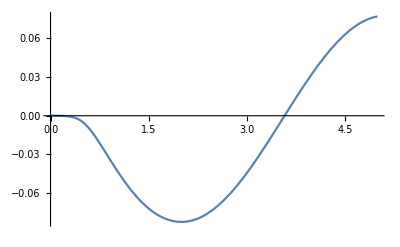

```mathematica
{TMin,TMax}={0,5};
x1Sol=NDSolveValue[{x''[t]+x'[t-1/2]+x[t-1]==0,x[t/;t<=0]==t^2},x,{t,TMin,TMax}]
Plot[x1Sol[t],{t, TMin,TMax}]
```

```mathematica
{TMin,TMax}={0,5};
x1Sol=NDSolveValue[{x''[t]+x'[t-1/2]+x[t-1]==0,x[t/;t<=0]==t^2},x,{t,TMin,TMax}]
Plot[x1Sol[t],{t, TMin,TMax}]
```

Systems

{InterpolatingFunction[…],InterpolatingFunction[…]}

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 25.}}, <>],InterpolatingFunction[{{0., 25.}}, <>]}

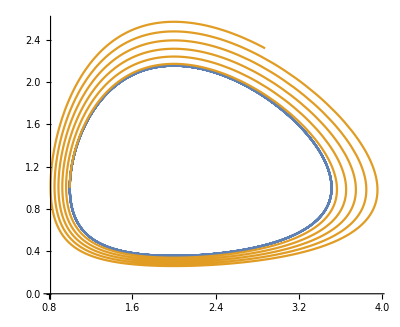

```mathematica
Clear[y,d1,d2,LVDelay]
LVDelay[d1_,d2_]:={
y[1]'[t]==y[1][t]*(y[2][t-d1]-1),
y[2]'[t]==y[2][t] *(2-y[1][t-d2]),
y[1][0]==1, y[2][0]==1};
tSwitch= 25;
{y1Sol,y2Sol}=NDSolveValue[LVDelay[0.0,0],{y[1],y[2]},{t,0, tSwitch}]
{y1Sold,y2Sold}=NDSolveValue[LVDelay[0.01,0],{y[1],y[2]},{t,0, tSwitch}]
ParametricPlot[{
{y1Sol[t],y2Sol[t]},
{y1Sold[t],y2Sold[t]}
},{t, 0, tSwitch}]
```

```mathematica
lv=First[NDSolve[lvsystem[0,0],{Subscript[Y,1],Subscript[Y,2]},{t,0,25}]];
lvd=Quiet[First[NDSolve[lvsystem[.01,0],{Subscript[Y,1],Subscript[Y,2]},{t,0,25}]]];
ParametricPlot[Evaluate[{Subscript[Y,1][t],Subscript[Y,2][t]}/. {lv,lvd}],{t,0,25}]
```

# Finding Periodic Sequences in 2D Smooth

For a function f:ℝ^2→ℝ^2  consider the sequence defined recursively by 
	p_(n+1)=f(p_n)
and an initial value p_0∈ℝ^2. We will make smoothness assumptions about f as we need them.  We learned that we will never see an unstable periodic orbit by iterating. We learned that a stable periodic orbit with a tiny stability region was also very hard to find!

Some pictures would probably help.

## Ex 1

The first thing we did in ℝ^1 was plot our function of interest with the “do-nothing” identity function.  This only worked because we had one spare dimension in which to plot.  We do not have two spare dimensions when we are in ℝ^2!

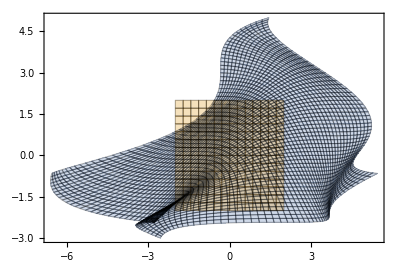

```mathematica
f[{x_,y_}]:= {0.1+x +2y+ Cos[x *y], y-x + Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

Then we decided we could plot get rid of the spare dimension by subtracting our function from the identity function.  We can now see that there is one fixed point:  The bad news is we have no idea which value of {x,y} it comes from!

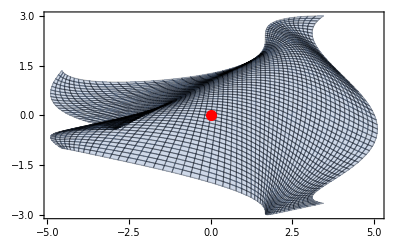

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

what we need to do is plot both coordinate bits that make the picture above together in a way that ties them back to the where they came from.  Not too bad!

```mathematica
Plot3D[{f[{x,y}]⟦1⟧-x,f[{x,y}]⟦2⟧-y},{x,-2,2},{y,-2,2},
PlotRange->{0, 5}]
```

-Graphics3D-

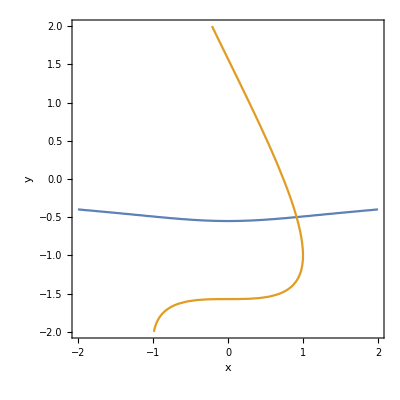

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed point!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,1},{y,-0.1}]
```

{x→0.91475,y→-0.498841}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know if this is stable.  First a picture.

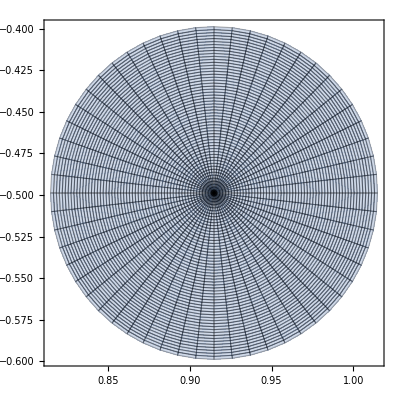

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ FP+r {Cos[θ],Sin[θ]},
{θ,0, 2π},{r, 0, 0.1},
Mesh->All]
```

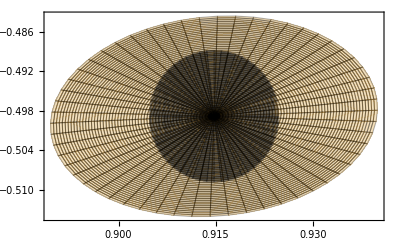

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.01},
Mesh->All,
AspectRatio->Automatic]
```

```mathematica
JMat=D[f[{x,y}],{{x,y}}]/.FPSub
Eigenvalues[JMat];
SingularValueList[JMat]
```

{{0.780189,2.40308},{-1.40402,0.595979}}

{2.53204,1.51615}

I do not think this is going to be a stable fixed point!

## Ex 2

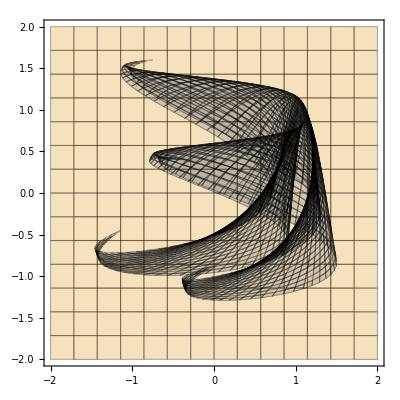

```mathematica
f[{x_,y_}]:= {0.1+0.2x +0.1y+ Cos[x *y], 0.1y-0.2x + Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

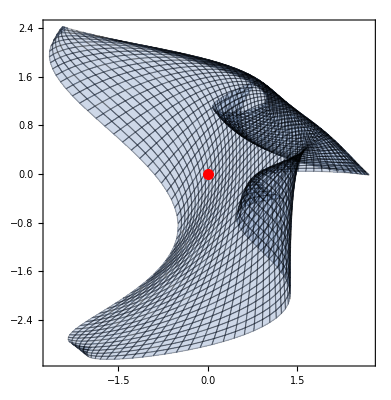

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

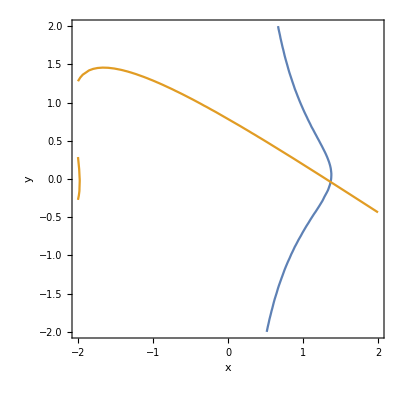

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed point!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,1},{y,-0.1}]
```

{x→1.3684,y→-0.0387445}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know if this is stable.  First a picture.

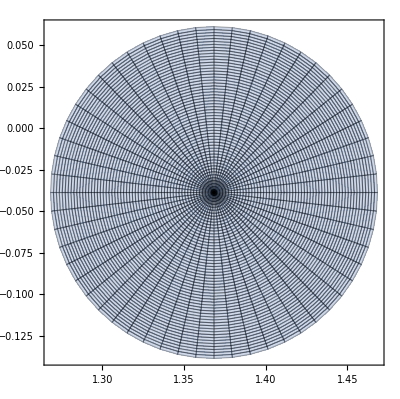

```mathematica
FP={x,y}/.FPSub;
ParametricPlot[ FP+r {Cos[θ],Sin[θ]},
{θ,0, 2π},{r, 0, 0.1},
Mesh->All]
```

{{-0.625817,-0.0473025},{1.4828,0.019964}}

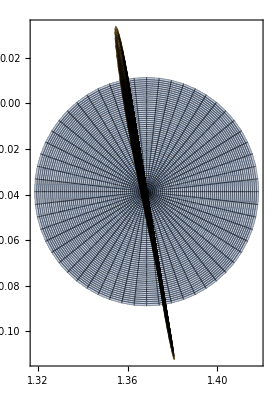

```mathematica
FP={x,y}/.FPSub;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

Still Not stable!

## Ex 3

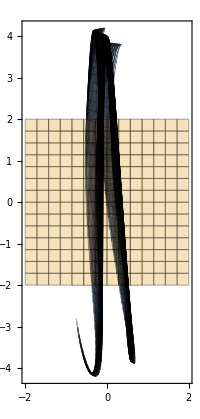

```mathematica
f[{x_,y_}]:= {0.2x +0.1y+ 0.2 Sin[x *y], 0.1y+ 4 Cos[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

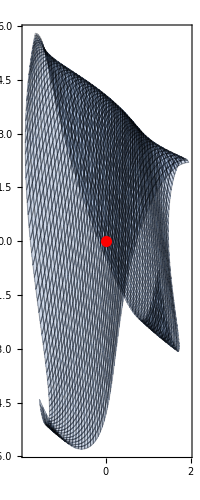

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

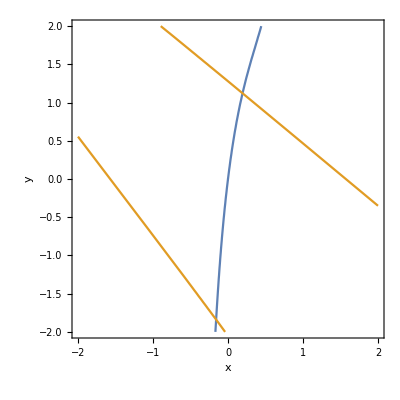

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed points!

```mathematica
FPSub1=FindRoot[f[{x,y}]=={x,y},{x,0},{y,1}]
FPSub2=FindRoot[f[{x,y}]=={x,y},{x,0},{y,-2}]
```

{x→0.194208,y→1.12149}

{x→-0.158191,y→-1.83927}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know which if any is stable.  First a picture.

{{-3.63901,0.287447},{5.41809,0.193061}}

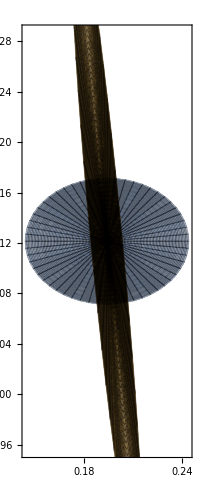

```mathematica
FP={x,y}/.FPSub1;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub1;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

{{3.80553,-0.216511},{5.22122,0.157806}}

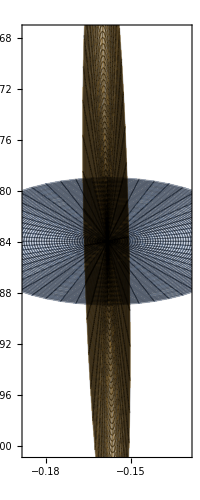

```mathematica
FP={x,y}/.FPSub2;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub2;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.05},
Mesh->All]
```

Still Not stable!

## Ex 4

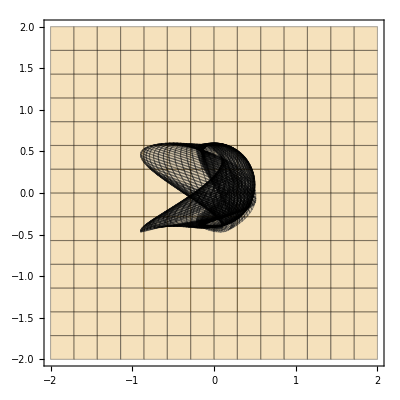

```mathematica
f[{x_,y_}]:= { 0.4 Sin[x *y]+0.5 Cos[x+2y], 0.1 Cos[x*y]-0.5Sin[x+y]}
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,2},{y,-2,2},
Mesh->All]
```

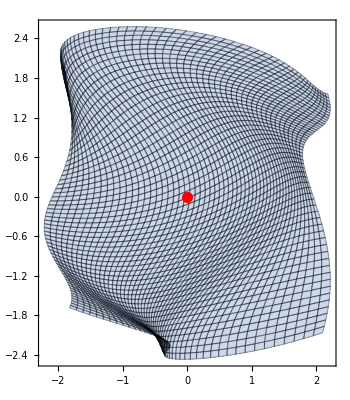

```mathematica
ParametricPlot[f[{x,y}]-{x,y},{x,-2,2},{y,-2,2},
Mesh->All,
Epilog->{Red, PointSize[0.02], Point[{0,0}]}]
```

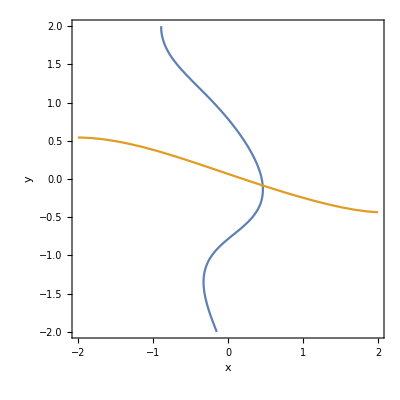

```mathematica
ContourPlot[{f[{x,y}]⟦1⟧==x,f[{x,y}]⟦2⟧==y},{x,-2,2},{y,-2,2},
Mesh->All,
FrameLabel->{"x","y"}]
```

Once we have a decent initial guess we can compute the fixed points!

```mathematica
FPSub=FindRoot[f[{x,y}]=={x,y},{x,0},{y,0}]
```

{x→0.462935,y→-0.0847117}

The bad news is we do not know if there are other solutions further out in x and/or y!   We would like to know which if any is stable.  First a picture.

{{-0.582792,-0.0585704},{0.686085,0.0497523}}

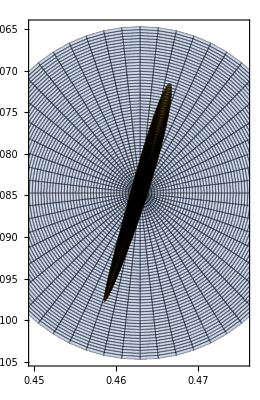

```mathematica
FP={x,y}/.FPSub;
JMat=D[f[{x,y}],{{x,y}}]/.FPSub;
{Eigenvalues[JMat],SingularValueList[JMat]}
ParametricPlot[ {
FP+r {Cos[θ],Sin[θ]},
f[FP+r {Cos[θ],Sin[θ]}]},
{θ,0, 2π},{r, 0, 0.02},
Mesh->All]
```

Stable!

```mathematica
ϵ=127.5; MaxIter=32;
p0=FP+ϵ RandomReal[{-1,1},2];
NestList[ f,p0,MaxIter] 
FP
```

{{-89.718,-62.7257},{-0.327199,0.446722},{0.363702,0.0393142},{0.457598,-0.0961074},{0.46491,-0.0769309},{0.461703,-0.0892233},{0.463602,-0.082048},{0.46253,-0.0862539},{0.463165,-0.0838093},{0.462798,-0.0852364},{0.463013,-0.0844055},{0.462889,-0.08489},{0.462961,-0.0846077},{0.462919,-0.0847722},{0.462944,-0.0846764},{0.462929,-0.0847322},{0.462938,-0.0846997},{0.462933,-0.0847187},{0.462936,-0.0847076},{0.462934,-0.084714},{0.462935,-0.0847103},{0.462934,-0.0847125},{0.462935,-0.0847112},{0.462935,-0.0847119},{0.462935,-0.0847115},{0.462935,-0.0847118},{0.462935,-0.0847116},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117},{0.462935,-0.0847117}}

{0.462935,-0.0847117}

# Building Simple Maps in 2D Non Smooth

The first thing we are going to look at is the puff pastry map a.k.a the Bakers map

## Bakers Map

This is a non-smooth map that is easy to understand.  It is puff pastry with a sharp knife.

```mathematica
Baker[{x_,y_}]:= Which[
0≤x<1/2, {2 *x,y/2},
1/2≤x≤1,{2-2 x, 1-y/2}
]
Vcolor=Function[{x,y,u,v}, Hue[u]];
Hcolor=Function[{x,y,u,v}, Hue[v]];
SetOptions[ParametricPlot,
MaxRecursion->0,
PlotPoints->{2^11+1,36}];
```

```mathematica
TabView[{
"Vertical Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Vcolor]
}],
"Horizontal Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Hcolor]
}]
}
]
```

12

## Rounded Bakers Map

I want to round of the Bakers map

BooleanRegion[#1||#2&,{Rectangle[{0,0},{1,1}],Disk[{0,1/2},1/2]}]

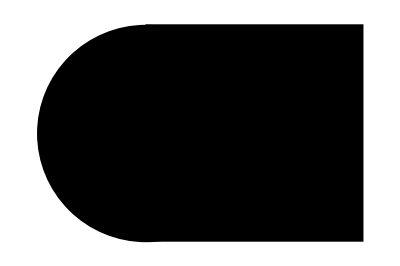

```mathematica
SmoothBaker[{x_,y_}]:= Module[{r,θ},
Which[
0≤x<1/2, {2 *x, y/2},
1/2<x≤1,{2*(1-x),1-y/2},
-1/2 <x<0, θ=ArcTan[x,y]; r= √((x+1/2)^2+y^2); Cos[θ]{2*x,y/2}+Sin[θ]{2*(1-x),1-y/2}]
]
Vcolor=Function[{x,y,u,v}, Hue[u]];
Hcolor=Function[{x,y,u,v}, Hue[v]];
SetOptions[ParametricPlot,
MaxRecursion->0,
PlotPoints->{2^11+1,36}];
Pill=RegionUnion[Rectangle[{0,0},{1,1}],Disk[{0,1/2},1/2]]
Region[Pill]
```

```mathematica
Graphics[Pill]
```

-Graphics-

```mathematica
TabView[{
"Vertical Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Vcolor]
}],
"Horizontal Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Hcolor]
}]
}
]
```

12